# Conformal factor falloff

```mathematica
M = 1;
```

## Schwarzschild (Isotropic coordinates)

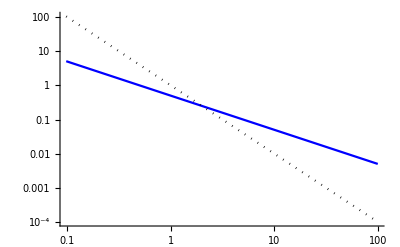

```mathematica
psi[r_] := 1 + M/(2 r)
LogLogPlot[{psi[r]-1, 1/r^2}, {r, 0, 100}, PlotStyle->{Blue, {Black, Dotted}}]
```

## Schwarzschild (Isotropic Kerr-Schild coordinates)

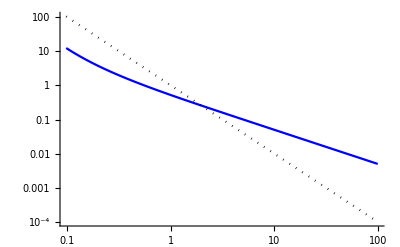

```mathematica
psi[r_] :=  (2 Exp[Sqrt[1 + 2 M / r] - 1])/(1 + Sqrt[1 + 2 M / r])
LogLogPlot[{psi[r]-1, 1/r^2}, {r, 0, 100}, PlotStyle->{Blue, {Black, Dotted}}]
```